Mathematica solution to foci of parabola.  We calculate the side lengths of the triangle formed by the reflected ray and the x-intercept of the line tangent to the point (x, alpha x^2) and use the Law of Cosines after computing the angle of reflection from Snell’s law.  Here s is Sin(theta).

```mathematica
c=Sqrt[x^2/(4)+h^2];
a=Sqrt[(x-x/(2 ))^2+α^2 x^4];
b = Sqrt[x^2+(α x^2-h)^2];
s=2 α x/Sqrt[4 α^2 x^2 +1];
Solve[c^2==b^2+a^2-2 a b s, h]
```

{{h→1/(4 α)}}

```mathematica
Clear[α]
```

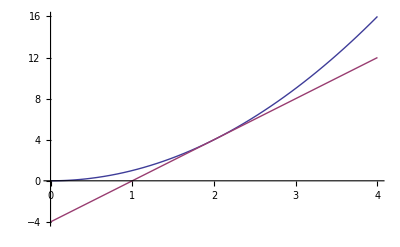

```mathematica
Plot[{x^2, 4x-4}, {x, 0,4}]
```